```mathematica
data=({{1, 0, 965, 72185, 190, 2454826, 12920.1}, {2, 0, 941, 76192, 203, 2616307, 12888.2}, {3, 10, 971, 68089, 178, 2952234, 16585.6}, {4, 20, 888, 73827, 362, 824413, 2277.4}, {5, 30, 735, 51589, 326, 291273, 893.5}, {6, 40, 679, 52698, 322, 208925, 648.8}, {7, 50, 604, 42443, 307, 160762, 523.7}, {8, 60, 522, 41123, 305, 137531, 450.9}, {9, 70, 459, 49867, 401, 160465, 400.2}, {10, 80, 411, 41004, 358, 131360, 366.9}, {11, 90, 365, 39560, 375, 129516, 345.4}, {12, 100, 332, 31455, 306, 101375, 331.3}, {13, 110, 307, 29843, 309, 100563, 325.4}, {14, 120, 302, 33041, 337, 106722, 316.7}, {15, 121, 664, 25445, 197, 99787, 506.5}, {16, 122, 835, 47502, 378, 196851, 520.8}});
```

```mathematica
plotData=Transpose[{N[1-Cos[data[[1;;14,2]]Degree]]}].({{1, 0}})+Transpose[{1/data[[1;;14,3]]}].({{0, 1}});
```

```mathematica
plotFit=LinearModelFit[plotData,x,x];
```

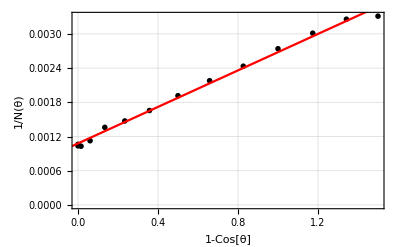

```mathematica
Show[ListPlot[plotData,PlotTheme->{"Detailed","Monochrome"},Frame->True,FrameLabel->{"1-Cos[θ]","1/N(θ)"}],Plot[plotFit["BestFit"],{x,-0.2,1.5},PlotStyle->Red]]
```

```mathematica
plotData
```

{{0.,0.00103627},{0.,0.0010627},{0.0151922,0.00102987},{0.0603074,0.00112613},{0.133975,0.00136054},{0.233956,0.00147275},{0.357212,0.00165563},{0.5,0.00191571},{0.65798,0.00217865},{0.826352,0.00243309},{1.,0.00273973},{1.17365,0.00301205},{1.34202,0.00325733},{1.5,0.00331126}}

```mathematica
N90=1/(plotFit["BestFit"]/.x-> 1);
N0=1/(plotFit["BestFit"]/.x-> 0);
```

```mathematica
N0
```

926.484

```mathematica
0.662*N90/(N0-N90)
```

0.446589

```mathematica
UnitConvert[Quantity[1,"ElectronMass"]*Quantity[1,"SpeedOfLight"]^2,"Kiloelectronvolts"]
```

510.9989 keV